# Pi Gate vs Zeeman Difference

Restart the kernel before evaluating this notebook.

```mathematica
ClearAll[
  pars1, pars2, parsint, Rot1, Rot2, Rotint, Jidle, H1, H2, Hint,
  makePars, sortedEigensystem, epsLogical, tPiUs, tPiNs, jIntPi,
  rebuildForDeltaFast, metricsAtDelta, deltaList, piScanData,
  UprojQS, oneSampleQS, averagedMetricsQS,
  noiseTrace1f, oneSample1fCorr, averagedMetrics1fCorr
];

n1 = {0, 1, 0};
n2 = {0, 1, 0};
nint = {0, 1, 0};

parsint = {θint -> 0.0};
Rotint = RotationMatrix[θint, nint // Normalize] /. parsint;

Rot1 = RotationMatrix[θ1, n1 // Normalize];
Rot2 = RotationMatrix[θ2, n2 // Normalize];

Jidle[gL_, gM_, gS_] := ((gM - gL)^2 - (2 gS - gL - gM)^2)/(2 (2 gS - gL - gM)) // N;

H1[J12_, J23_] := ((1/2) (
    g1 KroneckerProduct[PauliMatrix[3], PauliMatrix[0], PauliMatrix[0]] +
    g2 KroneckerProduct[PauliMatrix[0], PauliMatrix[3], PauliMatrix[0]] +
    g3 KroneckerProduct[PauliMatrix[0], PauliMatrix[0], PauliMatrix[3]]) +
   (1/4) Sum[
     J12 Rot1[[i, j]] KroneckerProduct[PauliMatrix[i], PauliMatrix[j], PauliMatrix[0]] +
     J23 Rot2[[i, j]] KroneckerProduct[PauliMatrix[0], PauliMatrix[i], PauliMatrix[j]],
     {i, 1, 3}, {j, 1, 3}]) /. pars1;

H2[J12_, J23_] := ((1/2) (
    g1 KroneckerProduct[PauliMatrix[3], PauliMatrix[0], PauliMatrix[0]] +
    g2 KroneckerProduct[PauliMatrix[0], PauliMatrix[3], PauliMatrix[0]] +
    g3 KroneckerProduct[PauliMatrix[0], PauliMatrix[0], PauliMatrix[3]]) +
   (1/4) Sum[
     J12 Rot1[[i, j]] KroneckerProduct[PauliMatrix[i], PauliMatrix[j], PauliMatrix[0]] +
     J23 Rot2[[i, j]] KroneckerProduct[PauliMatrix[0], PauliMatrix[i], PauliMatrix[j]],
     {i, 1, 3}, {j, 1, 3}]) /. pars2;

Hint[Jint_] := (Jint/4 Sum[
    Rotint[[i, j]] KroneckerProduct[PauliMatrix[0], PauliMatrix[0], PauliMatrix[i], PauliMatrix[0], PauliMatrix[0], PauliMatrix[j]],
    {i, 1, 3}, {j, 1, 3}]) /. parsint;

makePars[delta_?NumericQ] := {
  {θ1 -> 0.0, θ2 -> 0.0, g1 -> 53, g2 -> 74, g3 -> 47.0},
  {θ1 -> 0.0, θ2 -> 0.0, g1 -> 60, g2 -> 72, g3 -> 47.0 - delta}
};

sortedEigensystem[mat_?MatrixQ] := Transpose[SortBy[Transpose[Eigensystem[N[mat]]], First]];

epsLogical = -0.0001;

tPiUs[delta_?NumericQ] := Sqrt[3]/(2 Abs[delta]);
tPiNs[delta_?NumericQ] := 1000 tPiUs[delta];
jIntPi[delta_?NumericQ] := Abs[delta]/Sqrt[3];
```

```mathematica
rebuildForDeltaFast[delta_?NumericQ] := Module[
  {parsLocal, es1, es2},

  parsLocal = makePars[delta];
  pars1 = parsLocal[[1]];
  pars2 = parsLocal[[2]];

  j12Idle1 = N[Jidle[g1, g2, g3] /. pars1];
  j12Idle2 = N[Jidle[g1, g2, g3] /. pars2];
  j23Idle1 = 0.0;
  j23Idle2 = 0.0;

  es1 = sortedEigensystem[N[H1[j12Idle1 + epsLogical, j23Idle1]]];
  es2 = sortedEigensystem[N[H2[j12Idle2 + epsLogical, j23Idle2]]];

  eigval1 = es1[[1]] - es1[[1, 1]];
  eigvect1 = es1[[2]];
  eigval2 = es2[[1]] - es2[[1, 1]];
  eigvect2 = es2[[2]];

  gapIdle1 = eigval1[[3]] - eigval1[[2]];
  gapIdle2 = eigval2[[3]] - eigval2[[2]];

  eigtot = KroneckerProduct[eigvect1[[2 ;; 3]], eigvect2[[2 ;; 3]]];
  eigtotMatrix = N[Transpose[eigtot]];
  Pcomp = eigtotMatrix . ConjugateTranspose[eigtotMatrix];

  H1idle = N[H1[j12Idle1, j23Idle1]] // Chop;
  H2idle = N[H2[j12Idle2, j23Idle2]] // Chop;
  HidleFull = N[
    KroneckerProduct[H1idle, IdentityMatrix[8]] +
    KroneckerProduct[IdentityMatrix[8], H2idle]
  ] // Chop;

  HfullGate[Jint_] := N[HidleFull + Hint[Jint]] // Chop;

  Delta = (g3 /. pars1) - (g3 /. pars2);
  tGate[Jint_] := 1/Sqrt[Delta^2 + Jint^2];
  tGateNs[Jint_] := 1000 tGate[Jint];

  Utarget[Jint_] := Module[{tg, a, c},
    tg = tGate[Jint];
    a = 2 Pi Jint tg/4;
    c =  2 Pi Delta tg/2;
    DiagonalMatrix[{Exp[-I a], -Exp[I a + I c], -Exp[I a - I c], Exp[-I a]}]
  ];

  Uproj[Jint_] := Module[{tg, U},
    tg = tGate[Jint];
    U = MatrixExp[-I 2 Pi HfullGate[Jint] tg];
    ConjugateTranspose[eigtotMatrix] . U . eigtotMatrix
  ];

  gateFidelity[Jint_] := Module[{K, Uid, d = 4},
    K = Uproj[Jint];
    Uid = Utarget[Jint];
    Re[(Tr[ConjugateTranspose[K] . K] + Abs[Tr[ConjugateTranspose[Uid] . K]]^2)/(d (d + 1))]
  ];

  gateInfidelity[Jint_] := 1 - gateFidelity[Jint];

  avgLeakage[Jint_] := Module[{K, d = 4},
    K = Uproj[Jint];
    Re[1 - Tr[ConjugateTranspose[K] . K]/d]
  ];

  HdJ12Q1 = N[(1/4) Sum[
      Rot1[[i, j]] KroneckerProduct[PauliMatrix[i], PauliMatrix[j], PauliMatrix[0]],
      {i, 1, 3}, {j, 1, 3}] /. pars1] // Chop;
  HdJ12Q2 = N[(1/4) Sum[
      Rot1[[i, j]] KroneckerProduct[PauliMatrix[i], PauliMatrix[j], PauliMatrix[0]],
      {i, 1, 3}, {j, 1, 3}] /. pars2] // Chop;
  HdJ12Full1 = KroneckerProduct[HdJ12Q1, IdentityMatrix[8]];
  HdJ12Full2 = KroneckerProduct[IdentityMatrix[8], HdJ12Q2];
  HintFull = N[Hint[1.0]] // Chop;
];
```

```mathematica
sigmaJ12QS = 5.3*10^-4;
sigmaJintQS = 1.06*10^-3;
nSampQS = 200;

UprojQS[Jint_?NumericQ] := Module[{tg, d1, d2, dint, Hnoisy, U},
  tg = tGate[Jint];
  d1 = RandomVariate[NormalDistribution[0, sigmaJ12QS]];
  d2 = RandomVariate[NormalDistribution[0, sigmaJ12QS]];
  dint = RandomVariate[NormalDistribution[0, sigmaJintQS]];
  Hnoisy = HidleFull + j12Idle1 d1 HdJ12Full1 + j12Idle2 d2 HdJ12Full2 + Jint (1 + dint) HintFull;
  U = MatrixExp[-I 2 Pi Hnoisy tg];
  ConjugateTranspose[eigtotMatrix] . U . eigtotMatrix
];

oneSampleQS[Jint_?NumericQ] := Module[{K, Uid, d = 4, fidelity, leakage},
  K = UprojQS[Jint];
  Uid = Utarget[Jint];
  fidelity = Re[(Tr[ConjugateTranspose[K] . K] + Abs[Tr[ConjugateTranspose[Uid] . K]]^2)/(d (d + 1))];
  leakage = Re[1 - Tr[ConjugateTranspose[K] . K]/d];
  <|"Infidelity" -> 1 - fidelity, "Leakage" -> leakage|>
];

averagedMetricsQS[Jint_?NumericQ, nSamples_ : 200] := Module[{samples},
  samples = Table[oneSampleQS[Jint], {nSamples}];
  <|"Infidelity" -> Mean[samples[[All, "Infidelity"]]], "Leakage" -> Mean[samples[[All, "Leakage"]]]|>
];
```

```mathematica
noiseTrace1f[tg_?NumericQ, nSteps_ : 64, amp1Hz_ : 0., alpha_ : 1., window_ : 100] :=
  Module[{tObs, dt, df, t, f, phi, a},
    tObs = window tg;
    dt = tg/nSteps;
    df = 1./tObs;
    t = Range[0, nSteps - 1] dt;
    f = N[Range[1, Floor[window nSteps/2]] df];
    phi = RandomReal[{0, 2 Pi}, Length[f]];
    a = Sqrt[(amp1Hz^2/f^alpha) df];
    Table[Total[a Cos[2 Pi f tk + phi]], {tk, t}]
  ];

oneSample1fCorr[Jint_?NumericQ, ampJ12_ : 2.5*10^-4, ampJint_ : 5*10^-4, corr_ : 0.5, nSteps_ : 64, alpha_ : 1., window_ : 100] :=
  Module[{tg, dt, nCommon, nLocal12a, nLocal12b, nLocalInt, n12a, n12b, nint, U, K, Uid, d = 4, fid, leak},
    tg = tGate[Jint];
    dt = tg/nSteps;
    nCommon = noiseTrace1f[tg, nSteps, 1., alpha, window];
    nLocal12a = noiseTrace1f[tg, nSteps, 1., alpha, window];
    nLocal12b = noiseTrace1f[tg, nSteps, 1., alpha, window];
    nLocalInt = noiseTrace1f[tg, nSteps, 1., alpha, window];
    n12a = ampJ12 (Sqrt[corr] nCommon + Sqrt[1 - corr] nLocal12a);
    n12b = ampJ12 (Sqrt[corr] nCommon + Sqrt[1 - corr] nLocal12b);
    nint = ampJint (Sqrt[corr] nCommon + Sqrt[1 - corr] nLocalInt);
    U = Fold[Dot, IdentityMatrix[Length[HidleFull]], Reverse@Table[
      MatrixExp[-I 2 Pi dt (HidleFull + j12Idle1 n12a[[k]] HdJ12Full1 + j12Idle2 n12b[[k]] HdJ12Full2 + Jint (1 + nint[[k]]) HintFull)],
      {k, nSteps}
    ]];
    K = ConjugateTranspose[eigtotMatrix] . U . eigtotMatrix;
    Uid = Utarget[Jint];
    fid = Re[(Tr[ConjugateTranspose[K] . K] + Abs[Tr[ConjugateTranspose[Uid] . K]]^2)/(d (d + 1))];
    leak = Re[1 - Tr[ConjugateTranspose[K] . K]/d];
    <|"Infidelity" -> 1 - fid, "Leakage" -> leak|>
  ];

averagedMetrics1fCorr[Jint_?NumericQ, ampJ12_ : 2.5*10^-4, ampJint_ : 5*10^-4, corr_ : 0.5, nSteps_ : 64, nSamples_ : 20, alpha_ : 1., window_ : 100] :=
  Module[{samples},
    samples = Table[oneSample1fCorr[Jint, ampJ12, ampJint, corr, nSteps, alpha, window], {nSamples}];
    <|"Infidelity" -> Mean[samples[[All, "Infidelity"]]], "Leakage" -> Mean[samples[[All, "Leakage"]]]|>
  ];

ampJ12 = 2.5*10^-4;
ampJint = 5*10^-4;
nSteps = 100;
nSamples = 200;
alphaNoise = 1.;
window = 100;
```

```mathematica
metricsAtDelta[delta_?NumericQ] := Module[{Jint, mqs, m1f},
  rebuildForDeltaFast[delta];
  Jint = jIntPi[delta];
  mqs = averagedMetricsQS[Jint, nSampQS];
  m1f = averagedMetrics1fCorr[Jint, ampJ12, ampJint, 0., nSteps, nSamples, alphaNoise, window];
  {
    tPiNs[delta],
    delta,
    gateInfidelity[Jint],
    avgLeakage[Jint],
    mqs["Infidelity"],
    mqs["Leakage"],
    m1f["Infidelity"],
    m1f["Leakage"]
  }
];

deltaList = Range[1, 20, 0.1];
piScanData = Table[metricsAtDelta[delta], {delta, deltaList}];
```

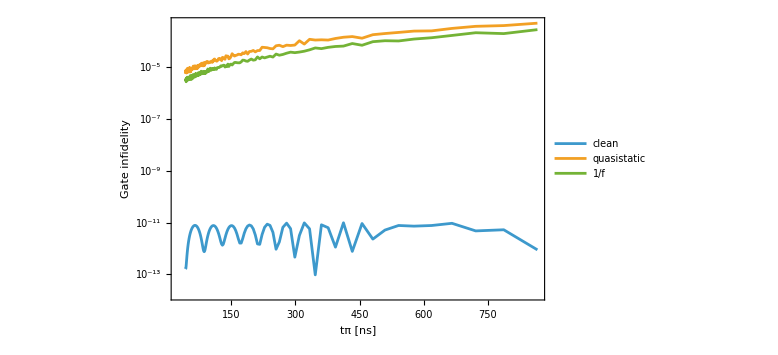

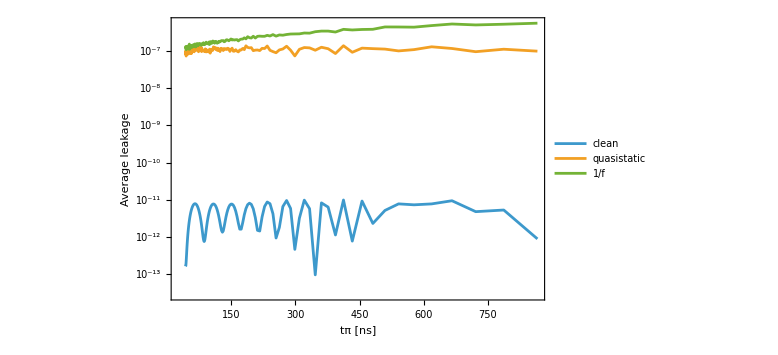

```mathematica
infidelityCleanPiData = piScanData[[All, {1, 3}]];
leakageCleanPiData = piScanData[[All, {1, 4}]];

infidelityQSPiData = piScanData[[All, {1, 5}]];
leakageQSPiData = piScanData[[All, {1, 6}]];

infidelity1fPiData = piScanData[[All, {1, 7}]];
leakage1fPiData = piScanData[[All, {1, 8}]];

ListLogPlot[
  {infidelityCleanPiData, infidelityQSPiData, infidelity1fPiData},
  Frame -> True,
  Joined -> True,
  FrameLabel -> {"tπ [ns]", "Gate infidelity"},
  PlotLegends -> {"clean", "quasistatic", "1/f"},
  ImageSize -> Large,
  PlotRange -> All
]

ListLogPlot[
  {leakageCleanPiData, leakageQSPiData, leakage1fPiData},
  Frame -> True,
  Joined -> True,
  FrameLabel -> {"tπ [ns]", "Average leakage"},
  PlotLegends -> {"clean", "quasistatic", "1/f"},
  ImageSize -> Large,
  PlotRange -> All
]
```

```mathematica
Export[
  "/Users/tivakhtel/SOSO-qubit/tess_code/pi_gate_vs_delta_scan.csv",
  Prepend[
    piScanData,
    {"tPi_ns", "Delta_g3_minus_g3prime", "clean_infidelity", "clean_leakage", "qs_infidelity", "qs_leakage", "onef_infidelity", "onef_leakage"}
  ]
];
```